## Setup

```mathematica
kellycols=RGBColor/@({{230,25,75},{60,180,75},(*{255,225,25},*){0,130,200},{245,130,48},{145,30,180},{70,240,240},{240,50,230},{210,245,60},{250,190,212},{0,128,128},{220,190,255},{170,110,40},{255,250,200},{128,0,0},{170,255,195},{128,128,0},{255,215,180},{0,0,128},{128,128,128}(*,{255,255,255}*),{0,0,0}}/255)
```

{RGBColor[{Rational[46, 51], Rational[5, 51], Rational[5, 17]}],RGBColor[{Rational[4, 17], Rational[12, 17], Rational[5, 17]}],RGBColor[{0, Rational[26, 51], Rational[40, 51]}],RGBColor[{Rational[49, 51], Rational[26, 51], Rational[16, 85]}],RGBColor[{Rational[29, 51], Rational[2, 17], Rational[12, 17]}],RGBColor[{Rational[14, 51], Rational[16, 17], Rational[16, 17]}],RGBColor[{Rational[16, 17], Rational[10, 51], Rational[46, 51]}],RGBColor[{Rational[14, 17], Rational[49, 51], Rational[4, 17]}],RGBColor[{Rational[50, 51], Rational[38, 51], Rational[212, 255]}],RGBColor[{0, Rational[128, 255], Rational[128, 255]}],RGBColor[{Rational[44, 51], Rational[38, 51], 1}],RGBColor[{Rational[2, 3], Rational[22, 51], Rational[8, 51]}],RGBColor[{1, Rational[50, 51], Rational[40, 51]}],RGBColor[{Rational[128, 255], 0, 0}],RGBColor[{Rational[2, 3], 1, Rational[13, 17]}],RGBColor[{Rational[128, 255], Rational[128, 255], 0}],RGBColor[{1, Rational[43, 51], Rational[12, 17]}],RGBColor[{0, 0, Rational[128, 255]}],RGBColor[{Rational[128, 255], Rational[128, 255], Rational[128, 255]}],RGBColor[{0, 0, 0}]}

```mathematica
thetaLines=Flatten[Table[{-Tan[#]μ,μ},{μ,(-√2.)/(√Tan[#]),0,((√2.)/(√Tan[#]))/(1000-1)}]&/@Range[(π/2)/(20.+1),π/2-(π/2)/(20.+1),(π/2)/(20.+1)],1];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"theta_points.csv"}],thetaLines]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\theta_points.csv

```mathematica
squareLines=Flatten[Table[{β,μ},{μ,0.5,1.,1./(100-1)},{β,Range[6,10]}],1];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"square_points.csv"}],squareLines]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\square_points.csv

```mathematica
DtD[dt_]:=Transpose[{First/@Drop[dt,1],Differences[Last/@dt]/Differences[First/@dt]}]
GetExps3[dt_,s_,c_]:=Module[{mx=dt[[First@Position[Last/@dt,Max[Last/@dt]]]][[1]][[1]],ldt1,ldt2,x},
ldt1=MovingAverage[Select[{Log[#1-mx],Log[#2]}&@@@dt,Im[#[[1]]]==0&&NumberQ[#[[2]]]&],s];
ldt2=MovingAverage[Select[{Log[mx-#1],Log[#2]}&@@@dt,Im[#[[1]]]==0&&NumberQ[#[[2]]]&],s];
-{LinearModelFit[ldt1[[#]]&/@(Position[First/@ldt1,#][[1]][[1]]&/@First/@Select[DtD@DtD[ldt1],Abs[#[[2]]]<c&]),x,x,ConfidenceLevel->0.99]["ParameterConfidenceIntervals"][[2]],
LinearModelFit[ldt2[[#]]&/@(Position[First/@ldt2,#][[1]][[1]]&/@First/@Select[DtD@DtD[ldt2],Abs[#[[2]]]<c&]),x,x,ConfidenceLevel->0.99]["ParameterConfidenceIntervals"][[2]]}]
```

## Processing

## Phase visualization

```mathematica
GCEgraph[lattice_,edges_,p_,l0_,β_,μ_]:=Graph@DeleteCases[RandomChoice[{1/(1+Exp[β(μ-(GraphDistance[lattice,#[[1]],#[[2]]]-l0)^p)]),Exp[β(μ-(GraphDistance[lattice,#[[1]],#[[2]]]-l0)^p)]/(1+Exp[β(μ-(GraphDistance[lattice,#[[1]],#[[2]]]-l0)^p)])}->{Null,#}]&/@edges,Null]
```

```mathematica
AllEdges[gg_]:=DeleteDuplicates[Sort/@Flatten[UndirectedEdge@@@Flatten[Subsets[#,{2}]&/@FindPath[EdgeDelete[gg,#],#[[1]],#[[2]],3,All],1]&/@EdgeList[gg]]]
```

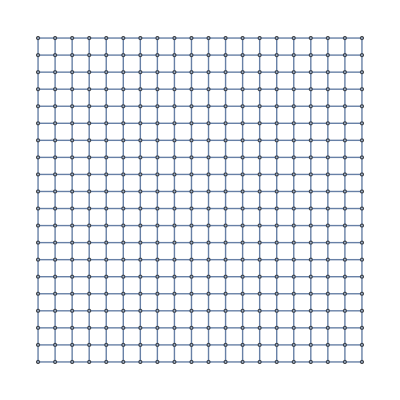

```mathematica
gg=GridGraph[{20,20}]
```

```mathematica
AbsoluteTiming[el=AllEdges[gg];]
```

{0.721378,Null}

```mathematica
phss=GraphicsRow[Rasterize[Quiet@Graph[VertexList[gg],EdgeList@GCEgraph[gg,el,2,1,#1,#2],PlotTheme->"LargeGraph"],ImageSize->400]&@@@{{10,-2},{1,-0.25},{0.,0.5},{10,0.5},{-5,-1}},ImageSize->1600]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","phases.png"}],phss]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\phases.png

```mathematica
Solve[p1==1/(1+ⅇ^(β μ))&&p2==1/(1+ⅇ^(β (μ-1))),{β,μ}]
```

{{β→ConditionalExpression[-2 ⅈ π C[1]-Log[(p1 (-1+p2))/((-1+p1) p2)], C[1]∈ℤ],μ→ConditionalExpression[-(2 ⅈ π C[2]+Log[(1-p1)/p1])/(2 ⅈ π C[1]+Log[(p1 (-1+p2))/((-1+p1) p2)]), (C[1]|C[2])∈ℤ]}}

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

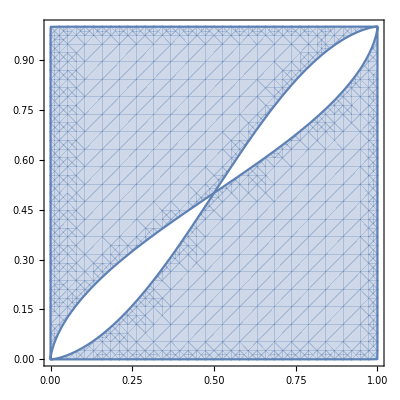

```mathematica
RegionPlot[-15<-Log[(p1 (-1+p2))/((-1+p1) p2)]<15&&-2<-Log[(1-p1)/p1]/Log[(p1 (-1+p2))/((-1+p1) p2)]<3,{p1,0,1},{p2,0,1}]
```

## Bond

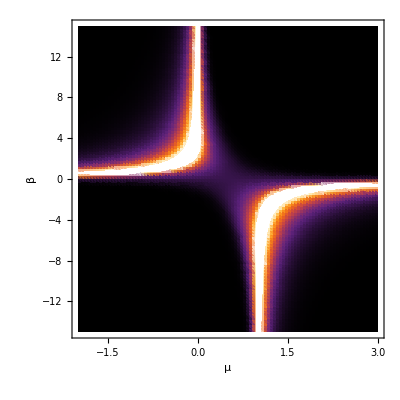

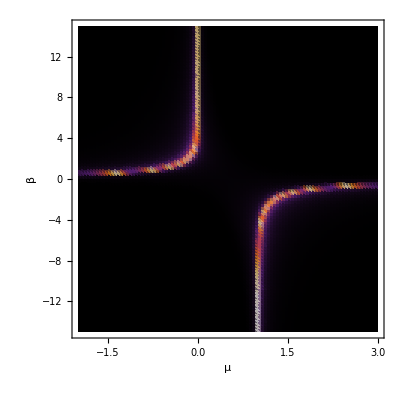

```mathematica
bplnlngths=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"outb_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ_b",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},PlotRange->{0,3}]
bplnlngths2=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"outb_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ_b",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","bondPlaneLengths.png"}],bplnlngths]
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","bondPlaneLengths2.png"}],bplnlngths2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\bondPlaneLengths.png

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\bondPlaneLengths2.png

### Theta

```mathematica
dt=Select[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"theta_points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"outb_200_1024_theta_points.csv"}]]}],#[[1]]!=0&];
ListPointPlot3D[dt,PlotRange->All]
```

-Graphics3D-

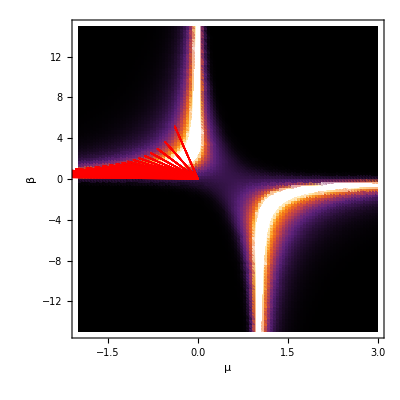

```mathematica
blines=Show[bplnlngths,ListPlot[{#1,#2}&@@@dt,PlotRange->{{-2,3},{-15,15}},PlotStyle->Red]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","blines.png"}],blines]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\blines.png

```mathematica
angs=DeleteDuplicates[Round[#,10^-3]&/@(-ArcTan[(#[[2]])/(#[[1]])]&/@dt)]
```

{3/40,3/20,28/125,299/1000,187/500,449/1000,131/250,299/500,673/1000,187/250,823/1000,449/500,243/250,1047/1000,561/500,1197/1000,159/125,673/500,1421/1000,187/125}

```mathematica
lbls=ToString[#,StandardForm]&/@(π/42*Range[20])
```

{π/42,π/21,π/14,(2 π)/21,(5 π)/42,π/7,π/6,(4 π)/21,(3 π)/14,(5 π)/21,(11 π)/42,(2 π)/7,(13 π)/42,π/3,(5 π)/14,(8 π)/21,(17 π)/42,(3 π)/7,(19 π)/42,(10 π)/21}

```mathematica
table[pairs_]:=TableForm[Partition[#1 *(#2":")&@@@pairs,4],TableAlignments->Center,TableSpacing->{0.1, 1}]
```

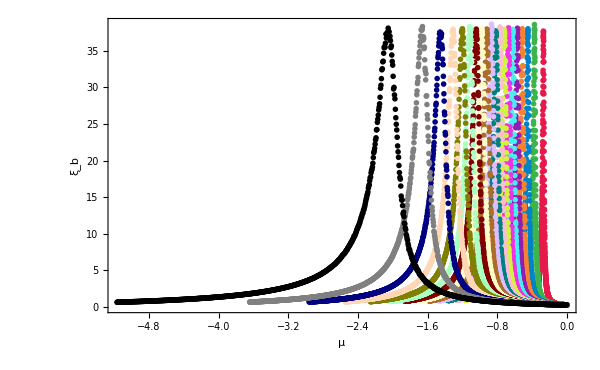

```mathematica
bdt=ListPlot[Table[{-#2,#3}&@@@Select[dt,Round[-ArcTan[(#[[2]])/(#[[1]])],10^-3]==angs[[i]]&],{i,20}],PlotRange->All,PlotStyle->kellycols,Frame->True,Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ_b",""},{"μ","β=-μ·tanθ"}},LabelStyle->Directive[Bold, 14],PlotLegends->Placed[LineLegend[kellycols,lbls,LegendLabel->"θ=",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->0,LegendLayout->table,LabelStyle->{Bold,FontSize->15},LegendMarkerSize->Small],{{0.01,0.98},{0.01,0.98}}],ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","bdt.png"}],bdt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\bdt.png

```mathematica
AbsoluteTiming[exps=Table[{angs[[i]],Interval/@Quiet@GetExps3[{#2,#3}&@@@Select[dt,Round[-ArcTan[(#[[2]])/(#[[1]])],10^-3]==angs[[i]]&],50,0.5]},{i,10}];]
```

{0.997084,Null}

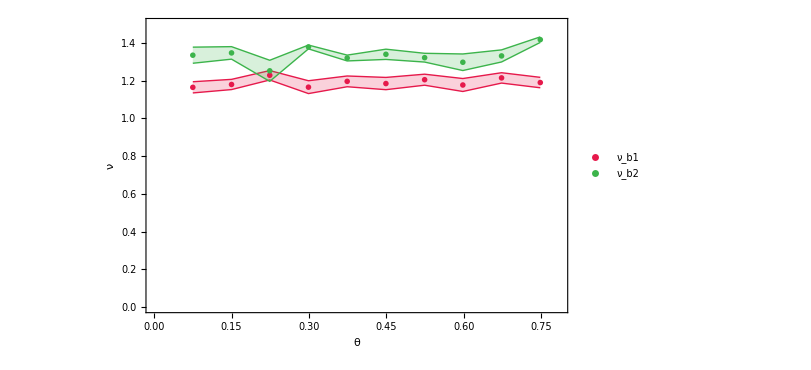

```mathematica
bexps=ListPlot[{{#1,#2[[1]]}&@@@exps,{#1,#2[[2]]}&@@@exps},PlotStyle->Take[kellycols,2],PlotRange->{{0,π/4},{0,1.5}},GridLines->{{},{4/3}},Frame->True,Axes->False,PlotMarkers->{"OpenMarkers",Medium},FrameLabel->{{"ν",""},{"θ",""}},PlotLegends->{"ν_b1","ν_b2"},LabelStyle->{Directive[Bold, 16],FontFamily->"Times New Roman"},ImageSize->600,IntervalMarkers->"Bands"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","bexps.png"}],bexps]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\bexps.png

## 0Site

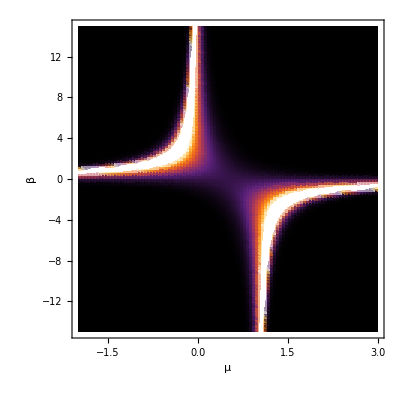

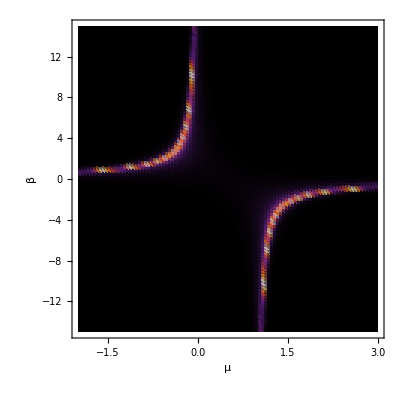

```mathematica
eplnlngths=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out0_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ_0",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},PlotRange->{0,3}]
eplnlngths2=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out0_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ_0",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","emptyPlaneLengths.png"}],eplnlngths]
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","emptyPlaneLengths2.png"}],eplnlngths2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\emptyPlaneLengths.png

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\emptyPlaneLengths2.png

### Theta

```mathematica
dt=Select[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"theta_points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out0_200_4096_theta_points.csv"}]]}],#[[1]]!=0&];
ListPointPlot3D[dt,PlotRange->All]
```

-Graphics3D-

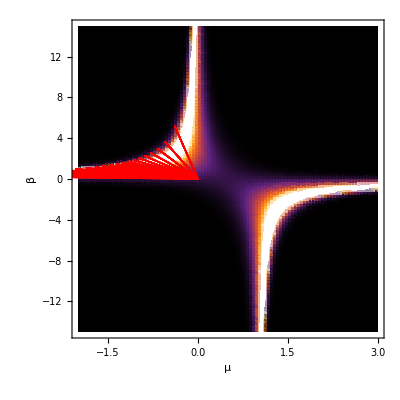

```mathematica
elines=Show[eplnlngths,ListPlot[{#1,#2}&@@@dt,PlotRange->{{-2,3},{-15,15}},PlotStyle->Red]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","elines.png"}],elines]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\elines.png

```mathematica
angs=DeleteDuplicates[Round[#,10^-3]&/@(-ArcTan[(#[[2]])/(#[[1]])]&/@dt)]
```

{3/40,3/20,28/125,299/1000,187/500,449/1000,131/250,299/500,673/1000,187/250,823/1000,449/500,243/250,1047/1000,561/500,1197/1000,159/125,673/500,1421/1000,187/125}

```mathematica
lbls=ToString[#,StandardForm]&/@(π/42*Range[20])
```

{π/42,π/21,π/14,(2 π)/21,(5 π)/42,π/7,π/6,(4 π)/21,(3 π)/14,(5 π)/21,(11 π)/42,(2 π)/7,(13 π)/42,π/3,(5 π)/14,(8 π)/21,(17 π)/42,(3 π)/7,(19 π)/42,(10 π)/21}

```mathematica
table[pairs_]:=TableForm[Partition[#1 *(#2":")&@@@pairs,2],TableAlignments->Center,TableSpacing->{0.1, 1}]
```

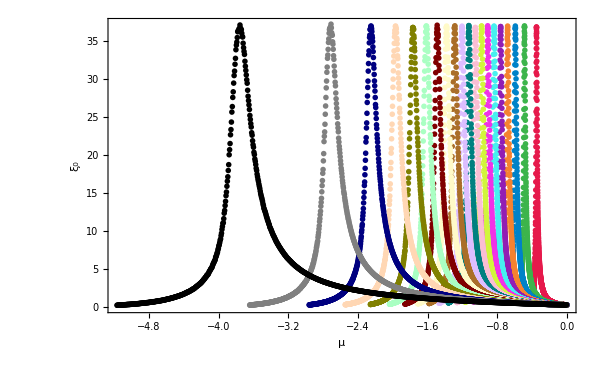

```mathematica
edt=ListPlot[Table[{-#2,#3}&@@@Select[dt,Round[-ArcTan[(#[[2]])/(#[[1]])],10^-3]==angs[[i]]&],{i,20}],PlotRange->All,PlotStyle->kellycols,Frame->True,Axes->False,PlotMarkers->{"OpenMarkers",Small},FrameLabel->{{"ξ_0",""},{"μ","β=-μ·tanθ"}},LabelStyle->Directive[Bold, 14],PlotLegends->Placed[LineLegend[kellycols,lbls,LegendLabel->"θ=",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->-4,LabelStyle->{Bold,FontSize->15},LegendMarkerSize->Tiny,LegendLayout->table],{{0.01,0.99},{0.01,0.99}}],ImageSize->600]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","edt.png"}],edt]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\edt.png

```mathematica
AbsoluteTiming[exps=Table[{angs[[i]],Interval/@Quiet@GetExps3[{#2,#3}&@@@Select[dt,Round[-ArcTan[(#[[2]])/(#[[1]])],10^-3]==angs[[i]]&],50,0.5]},{i,10}];]
```

{1.01643,Null}

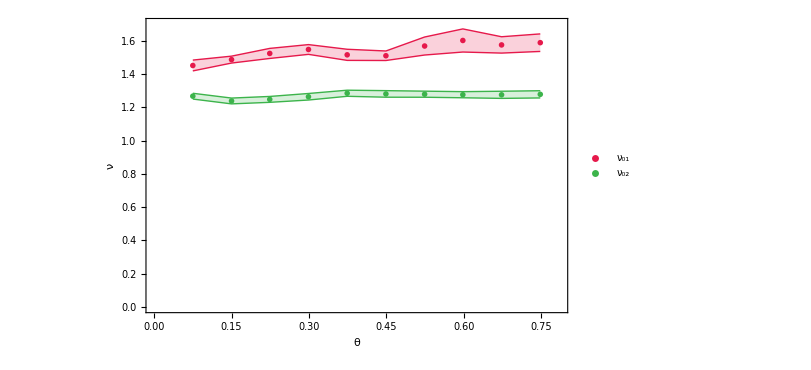

```mathematica
eexps=ListPlot[{{#1,#2[[1]]}&@@@exps,{#1,#2[[2]]}&@@@exps},PlotStyle->Take[kellycols,2],PlotRange->{{0,π/4},{0,1.7}},GridLines->{{},{4/3}},Frame->True,Axes->False,PlotMarkers->{"OpenMarkers",Medium},FrameLabel->{{"ν",""},{"θ",""}},PlotLegends->{"ν_01","ν_02"},LabelStyle->{Directive[Bold, 16],FontFamily->"Times New Roman"},ImageSize->600,IntervalMarkers->"Bands"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","eexps.png"}],eexps]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\eexps.png

## 4Site

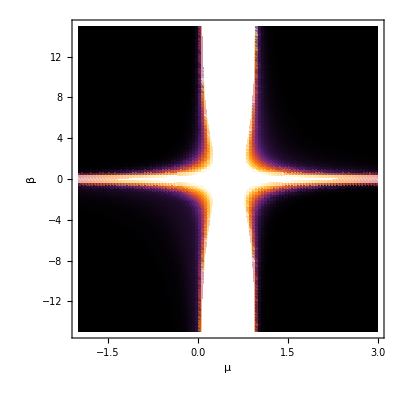

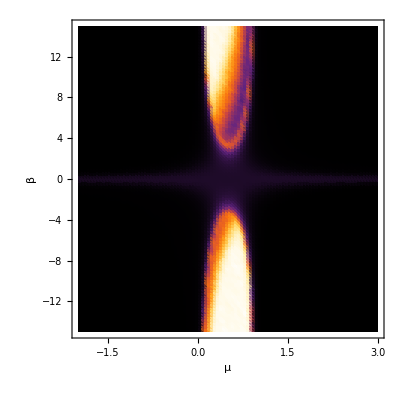

```mathematica
fplnlngths=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out4_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ_4",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},PlotRange->{0,3}]
fplnlngths2=ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out4_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ_4",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","4sitePlaneLengths.png"}],fplnlngths]
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","4sitePlaneLengths2.png"}],fplnlngths2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\4sitePlaneLengths.png

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\4sitePlaneLengths2.png

### Mu scan

```mathematica
dt=Select[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"square_points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out4_800_1024_square_points.csv"}]]}],#[[1]]!=0&];
ListPointPlot3D[dt,PlotRange->All]
```

-Graphics3D-

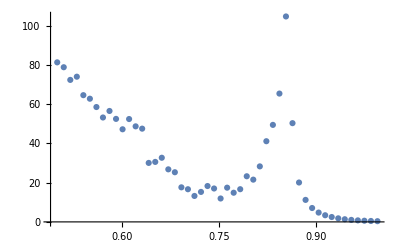

```mathematica
ListPlot[{#[[1]],#[[3]]}&/@Select[dt,#[[2]]==9&]]
```

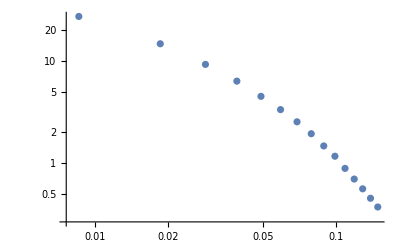

```mathematica
ListLogLogPlot[{#1-0.845,#2}&@@@Select[{#[[1]],#[[3]]}&/@Select[dt,#[[2]]==8&],#[[1]]>=0.85&]]
```

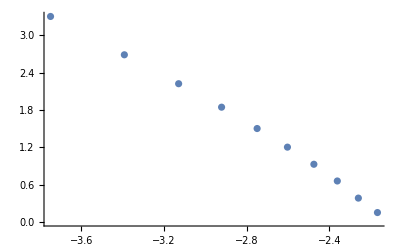

```mathematica
ListPlot[{Log[#1-0.83],Log[#2]}&@@@Select[{#[[1]],#[[3]]}&/@Select[dt,#[[2]]==8&],0.95>=#[[1]]>=0.85&]]
```

```mathematica
LinearModelFit[{Log[#1-0.78],Log[#2]}&@@@Select[{#[[1]],#[[3]]}&/@Select[dt,#[[2]]==6&],0.9>=#[[1]]>=0.8&],x,x]
LinearModelFit[{Log[#1-0.8],Log[#2]}&@@@Select[{#[[1]],#[[3]]}&/@Select[dt,#[[2]]==7&],0.92>=#[[1]]>=0.82&],x,x]
LinearModelFit[{Log[#1-0.83],Log[#2]}&@@@Select[{#[[1]],#[[3]]}&/@Select[dt,#[[2]]==8&],0.95>=#[[1]]>=0.85&],x,x]
```

FittedModel[-2.69733-1.6466 x]

FittedModel[-3.87713-2.10957 x]

FittedModel[-4.03023-1.98451 x]

```mathematica
ListPlot3D[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out4_800_8_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],PlotRange->{0,20}]
```

-Graphics3D-

## Output

## Temp

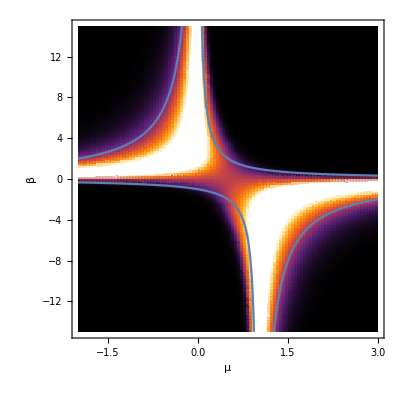

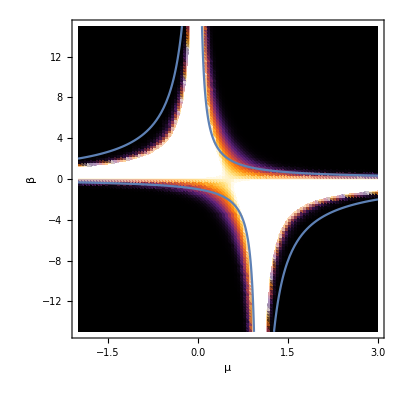

```mathematica
Show[ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"outb_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"}],Plot[{1/x},{x,0,3},PlotRange->15],Plot[{1/(x-1)},{x,-2,1},PlotRange->15],Plot[{-4/x},{x,-2,0},PlotRange->15],Plot[{-4/(x-1)},{x,1,3},PlotRange->15]]
Show[ListDensityPlot[{#1[[2]],#1[[1]],#2}&@@@Transpose[{Import[FileNameJoin[{NotebookDirectory[],"points.csv"}]],Flatten@Import[FileNameJoin[{NotebookDirectory[],"out0_200_512_points.csv"}]]}],ColorFunction->"SunsetColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"ξ",LabelStyle->{Directive[Bold, 14]}],Above],ImageSize->400,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"}],Plot[{1/x},{x,0,3},PlotRange->15],Plot[{1/(x-1)},{x,-2,1},PlotRange->15],Plot[{-4/x},{x,-2,0},PlotRange->15],Plot[{-4/(x-1)},{x,1,3},PlotRange->15]]
```

## Presentation

```mathematica
shrtcts=Rasterize[Graph[{2<->6,3<->7,5<->6,6<->7,6<->10,7<->8,7<->11,9<->10,10<->11,10<->14,11<->12,11<->15,6<->11,7<->10},VertexCoordinates->{{1,0},{1,1},{2,0},{2,1},{0,1},{1,2},{3,1},{2,2},{0,2},{1,3},{3,2},{2,3}},EdgeStyle->{6<->11->{Red,Dashed,Thick},7<->10->{Red,Dashed,Thick}}],ImageSize->600,ImageResolution->600]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","shortcuts.png"}],shrtcts]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\shortcuts.png

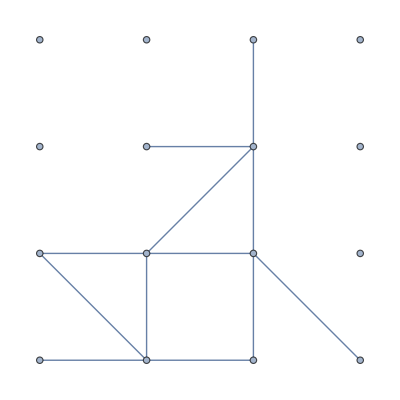

```mathematica
eg=Graph[Range[16],{1<->2,2<->3,4<->7,2<->5,2<->6,3<->7,5<->6,6<->7,6<->11,7<->11,10<->11,11<->15},VertexCoordinates->Flatten[Table[{j,i},{i,4},{j,4}],1]]
```

```mathematica
clusts=GraphicsRow[{HighlightGraph[eg,Style[Subgraph[eg,{1,2,3,4,5,6,7,10,11,15},Red]],VertexSize->Small],
HighlightGraph[eg,Style[Subgraph[eg,{2,6,7,11},kellycols[[1]]]],VertexSize->Small],
HighlightGraph[eg,{Style[{9,13,14},kellycols[[1]]],Style[{8,12,16},kellycols[[2]]]},VertexSize->Small]},Frame->All]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","clusters.png"}],clusts]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Final Project\Report\figures\clusters.png